```mathematica
(*path = "/home/clarissa/Downloads/metcompc/Ising/Ising/";*)path = "/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Ising/Ising/";
data = Import[path <> "Ising" <> StringTrim@ToString@PaddedForm[#//N,{2,1}] <> ".txt", "Data"]&/@{1.0,2.3,10.0};
```

```mathematica
labels = {"T = 1.0", "T = 2.2692", "T = 10.0"};
Manipulate[ListPlot[GatherBy[Take[data[[T]],{i*100+1,(i+1)*100}],#[[3]]==1&][[All,All,{1,2}]],PlotStyle->{{Red,PointSize[0.03]},{Blue,PointSize[0.01]}},Axes->False, PlotLegends->{"down", "up"}, PlotLabel->labels[[T]]],{i,0,2000,1,AnimationRate->50}, {T, {1,2,3}}]
```

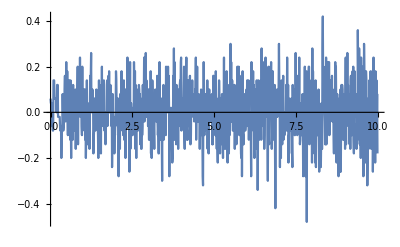

```mathematica
ListLinePlot@Import[path <> "Ising_Magnetization.txt", "Data"]
```

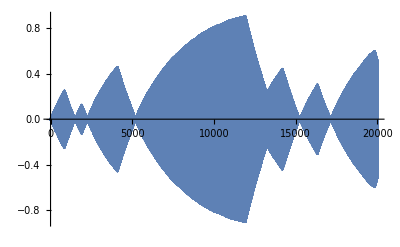

```mathematica
ListLinePlot@Import[path <> "IsingMagnetizationEquilibrium.txt", "Data"]
```